This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 5 Accuracy profiles of central power expansions ch5CentralProfiles.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Compute/Retrieve singular data

### Section 2.1: Compute singular data

```mathematica
$workingPrecision=1000;

at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=getSingularPoints[$theFunction,$workingPrecision,True];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];
$singularPerimeters=$minRadiusArray;
$singularNorms=$rNormArray;
$singularDistances=$nearestDistanceArray;
(*
 add 0 for TestCase0006 for book
*)
(*If[subDirectory=="testCase0006",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];*)
(*
 add 0 for testCaseFInif
*)
(*If[subDirectory=="testCaseFInif",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];
*)
If[subDirectory=="testCase0001Inf0",
singPerim=1/3 Abs[$theSingularList[[1]]];
PrependTo[$theSingularList,0];
$minRadiusArray={singPerim,singPerim,singPerim};
];
If[subDirectory=="testCase0400",
$theSingularList={0,1};
$minRadiusArray={1/3,1/3};
$poleIndexes={};
];




Print["Total singular points: ",Length@$theSingularList];
Print[Style["Time to compute singular points: ",Red,Bold],at[[1]]];
singPrec=Floor@Precision@$theSingularList;
If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
N[$theSingularList[[1;;2]],20];
];

 Export[singularDataFileName[$theTestCase],{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}];
Export[resultantFileName[$theTestCase],res];

aForm[$theFunction]
Grid[g2]
```

Time to compute resultant: 0.0018576

Time to compute singular points: 0.0065971

Total singular points: 10

Precision of singular points: 1000.

Total poles: 0

Pole indexes: {}

Total zero points: 0

Zero indexes: {}

Min singular perimeter: 0.119719

Smallest singular points: {0.,-0.33719-0.426404 ⅈ}

Total singular points: 10

Time to compute singular points: 0.0130578

Zero is a singular point

minSingAccFactor: 5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Grid[g2]

### Section 2.2: Retrieve singular points

```mathematica
(*
 retrieve singular points from disc
*)
If[FileExistsQ[singularDataFileName[$theTestCase]],
theData=Import[singularDataFileName[$theTestCase]];
{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=theData;

Print["Total singular points: ",Length@$theSingularList];

Print["Precision of singular points: ",Precision@$theSingularList];Print["Total poles: ",Length@$poleIndexes];
Print[Style["s_p indexes: ",Red],Style[$poleIndexes,Red]];
Print[Style["s_z indexes: ",Red],Style[$zeroIndexes,Blue]];

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
If[$theSingularList[[1]]==0,
Print["Smallest sing power: ",N[$theSingularList[[2]]^maxZ,10]];
,
Print["Smallest sing power: ",N[$theSingularList[[1]]^maxZ,10]];
]; 
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
(*res=Import[resultantFileName[$theTestCase]];*)
(*
 get reformed funtions
*)
(*Print["Retrieving reformedFunctionTable . . ."];
reformedFunctionTable=Import[reformedFunctionTableFileName[$theTestCase]];*)
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

Total singular points: 10

Precision of singular points: 1000.

Total poles: 2

s_p indexes: {1,8}

s_z indexes: {2,3}

Smallest sing power: -0.25

minSingAccFactor: 5

### Use AsymptoticSolve to compute series

{45.0828,Null}

(-1.03078752567445731922036302713958402167206294512565620770068252843097350518763810105414591305996393751265667937377068716760248588019215124518737570479914369371256869707363246996328770412742301122583746761198265128500061526025770251520674604136490677330866184617737903763065260096381405333298305432940823767067829813150402275085740325559160243423449055003105286944997647596223266117594962644957664032538710450761250089767638401101618263977477910055761128937241530074781583576275993611124032275829470821633266302172152999054800611178015363923380388979777703283069818292699330969522933285297524098829780490891962354979426796240929843503096040446889205554311150081465896528715736737692181865983840100888484089029744904533196013391138394046150909684299558660309153214470173882440355320065351354286859411986199795091531391932658407284558027327390551277111266911728297043863156292157181576920756314873004350933647739605887037926710044331327004313439831187887524991663076180852618824640961864275724737112687639635168681031+0.10489161204031145673306123259607605442325038762405562366907837400001917669638419999477133201731245582919378579906860488191264201712870324337808885203165147817107643301034829764945122888851332774428917393106661076129738544803731608352828595951616003424031810556699859956460453732037796297759574207887119893717443948475079184060303609181934991390716427236093241918794031322786459389045352868292120278358349189434794109212177091308899057471818248278253673673003432560814174156424390687593843534411123417424600002437201135373496932702267167227497058120485668915675724428057514319585430194679316485285750012226322227097923120874597517088941116115217798140560212713269282527012180387261881890164454287968836676652395712746701992419056197281926659674617359227597999482882013460496324930997761739126435717075519704833181107253454885512005710208380891645117982694495112819872248810763593626576414103093598888908291063757175131264650805913397369507916147826195272404845829453966433267842228933107756761313547727566252208145 ⅈ)-(0.4571013197266286875690156059730980841911020517404015599083737596924492196689963894782708531554625919041568534487666128614020432478975188331739205552844538642542914484647152371033578400318535537294697033069858860191071515813352228384841083198177572186706214174187659035542548190002354047738950900163129317582076855005546575209744255628631800600493051493129989270897437139270084599083042603641842968108389646934882806280713504017208183722749811354963466239622009660980217822373745182472720477573392540351051763892256045269271592426071679216002135703323591936769054782302482130693163137428347839675143768874447276598309237675397523579645771512859775432804430672809717346104835655573502313696757618608623244631064644559200827892420779962524409710908697485856532328127715338311424913595694264237845778356962696610139891689042215432165899857506052034026307636517442195246013779095942281065920625922471920947791020637480768060995979246124800415950316457700051008972694631974766498546498677984779472629828068141485794-0.06090126749259226284607911665439478804645125626243943987913439619236438008663998351812163153344701953338473860066755552039971700527299011007816198227066054447331146407168901998756416710063332623075455192384289424514992132888221452509400827891559803110887520569145330449163269975728100256629614205451465915823910734938242061821363300183981125999953039276110359952271848143012684970514187247730367688063559265376086537209106392064690702362167254443000852550459193089620854124494010632651970836193250062531062710556551311771017311854145440230917278339047801038049059388665582485810161265803614771838470637592574300557049772656387375287193840281383093605611954652280418305507054799589799924502139971558340386275745728457454940697368004387688529694328977989075867147329535823398264670808893609462969941245519880532977766728624379004781919829358510638762100731820106884074139179975804084610843169751003181044124212667864487876401456820140278065797032731936296447031702680195434972438018266104166503112826619786049858 ⅈ) ((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z)-(4.50601559333702331263286078591312417961690382179837578359679369715972505231825834184963928486512003563051266890154352917602266132657151893371208452336881792307113499934265380402784087790758715444215899505024875543316061000916555363292743029935767529758215784331992503239161568031405624540138303845095221540827884478048088778437066393095549768253522118292027634451325570648971140787091615415515216674784793851018836040439780218430524632457887869348304029512001907539540573168074450765433224617687597681047009746077084693222754976461876328030416963577550631513367146884897670118804955004686933351069360927720689233593917963470856250813582658811907511550924978819268597920145503857468583955765369262955998920504966936961662077065977101110419704361654570684024042547872875563492887525236606503138246356525560178056828777355574891543329005327645091787158130144029949262580725877924949156849248056304935667491683227078859166843398426503152794768810712806883037823831012471864476592615120128216435841882803194500759-2.14195430313680038570464420287156330884915468003995103096524898323880224163338081223309932522485835650685015628365130134042676655333796579995944647590958315375362016685374073537816279464784543853001260083906189951385053120772213060596463141768783090514020410335407350126496772046209097874320572245778498478439174703791587591148078889287630119233283571709456989508768021612784215986888189133564379122423053294595529743060146111078708033921745204341295250551149712730036556424080930603720115282046132409676647385924127643790535374145434346506410599494650095131502104671368893141438036031201226661798985733710425814925482462170772946598123737717059987959837233621702781864612780041224651984139892562157127776593273900828703277714354775172618240760576005598301805658983222009467071989459840288407462736262054324500864022932595357427177405201831785475649032025003504120370692409226579646605913207976496774688662521969232559697469641086236241040390731849947853038616131105438192421873212774936358973554590116591018 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^2-(1.501324907012804852253108285031894071677413928022324801913106518053765903413387135279836507893721286301998093616558192903525613598178875992729512063381348525937316809688387499218634944301283090691626794092316126527684299996414270670672611960228439054284764050345162445419144578889177964280984922502600452657729619897967579085751484725401348383276337435878801883604916363121488669328699365547399517120862680787683623243335403482200985124485950856842963452396867977240341465161569438342166527435423171536147863469438416158421452209405732702556849319650856035020706015143487627679802967712091273699865057579850071889560692544959912169079502105415904766425648141616746642492656968770915734097076389201788898014666712044022401744680266493248564936833139095681965021998783634334214455317584142031170887368847578485283031862340563064403647119717899287177658436838158185535695252222002771393899416252836306353328315545520211032828054590495558706580368438052220995021861715579320041498948026304574273583219146852533-2.163022430420441385681093060971714733550994088273991866948263222361510176617277516856992811969938059657279820693990979795145638501382857348238458527976598880819329186848358779527846628276430372265409417223825897358420388842605214697874366618462738191347845685513991345860451383031348820646999178555199629797325471100174650524278380590898642365467680513995965798234398192935463566172562483429256468758334585434391272822237054564754170555579928443436836276874309119142277466100572239200279626532809289668615342941065763687288112941875747012455906867329960774704570927766837105375119367499580666804249687446283291789013853634478610684601955661281751005426224429630132598265622766948246853433449235129466347353376974298981567322146302004555186462812675173551715773604405919199639181298301721315345947660227756972891508396146083523981357415999199096390247802937570091765799554416175816237238397506360677984955860383733419963109632513102821102385753002733057934581728448304007057148054147330904646770661673609721 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^3-(4.728323090850902394952682360396189538912340520226400665681449682297436699193308805358925759860435129827316143136367245941405056516578332861383568152278066106976914765363605982471206288127716298137400937788436817973940724574426408850907265159076261586212523226264887468563903707217483803961627702722469974408957449636957916610800430194273104611653764585733388320175288242139404739002342389401476947641685829531034934543030832349498492143516635506007589851688335122343791534634730802746167388658793193498779629164851063354318194323381135174766959167377506118903270138968392734673458073575089443993767635276073701485022945308636788254944828623681826031302656547912160562406737873698935130851824576925509436948175430455447941519070597525484173371349117416348482880398644842783386338541684354020368602448229933085911957133590709500340476256621445038950439854455585246101024836961502803375667237051902851234655738434237855308580744545940380742592689700997072660359171843996211545702903834327290427142038418448+317.3692931206124134054968789884011416875740495422167125367627142705229535753702541828215708418257732741421462845295639446233727605007607000160063509270121271369091757233856003203433981858404037320343164455659512274828158770586228335897917180429086051924926823909154795723838357582729082025762818990279872228890916919997040270170863892459586018868801425678222709271547863190589487231091852557587602512173214009508565825989874862414305137833140296311291567520096227397149458490797356068110349120543189361837919851374624265947461037145842739854909092719910673296165407021463020429076111506184869156205983061314816267630516169305034374287502621557897752964855591168416946326778130856600110676700470513369274662502912343190403697524228307502148675030695538244763152357880393137271072407260267986362514114481295454942276910359827422391150457888485184329575830949390042900645116112519078795931276835669440159531334512056420568777271056051629083040430892806183739219278460800894580277972334419124753793923634870343 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^4-(1507.07514535659155282549918838100347528124120991362671333687692972671315485556023297701847981656037367166010168356119642017373879365007687425459450418891907312255754571512540592960205331955121782457851124106022792759811709655671988183805461871435437988363998068054932844735839246922560876363422139384593520324907101428341934288200595957257293064198131724843287633381822361107931451365559729086960344004821789341958262866267644173859587758363575704089121372556148200324399297066156530710950227670362148996901667395970962371490509462003066963402242659449741651710703059582115486609805414261116501260476556187386024626891519796174318251812273851665768335753642854010112258423125871101978274254449336414013409509567164892987762600140086565642281395527911935982119722585564309699775975910400448629569930651469067445759228600293761229352765325614863609638234228601881888324167966386052023490928797089841693045293236491227631327424171025202447430021467901633710703880143464901707679122058533268533632123955433472+699.797504134967684089429061474992142444468041123681467680174397028420125812316249150070631682982447491517767018657087951265821473761950358688873955030808370702509343565729825676009495934772154602647021703570573085400462207659530174179816157144525206139460954787457673539477176896834814807562061613800745247167331480630270267588380486207174136580406962415135024031212608136068515076806435575706831524042254301272666697824072127320160948056869535033796180068008663544020738630825840048862409593945505434200283323125820148910900357008254262104628106878168154279411569768938791797332997309527482321673495513248422324876097804720136266570125832468356185980686981986203917047923904944337021949479669760850179769669271836180191583038596994721008633370390364339597074166395418627009753107485330622992390578255218068402215304124479315662322858881301153356447421885491585421189583076274461863880636901933506266101026004354953742881620050979219141083820212451161632256253632008795038891778716344182170384590507185904 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^5

```mathematica
mmSeries[[1]]
```

-(-5/3)^(1/9) z^(4/9)-1/36 (-5/3)^(1/9) z^(13/9)+1/324 (-5/3)^(1/9) z^(22/9)-(17 (-5/3)^(1/9) z^(31/9))/34992+(116861 (-5/3)^(1/9) z^(40/9))/2519424

```mathematica
(* end of section *)
```

## Section 3: Select base singular point

Select a desired singular point to analyze its accuracy profiles

```mathematica
baseSingularIndex=2

 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
Print["baseSingularPoint: ",$theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
Print["Len dataList: ",Length@dataList];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
(*
 report data in file:
*)
Print["baseRemovableList: ",baseRemovableList];
Print["baseSeries precision: ",Precision@baseSeries];
Print["baseSheetLinks: ",baseSheetLinks];
Print["Chosen singular point: ",N[baseSingularPoint,25]];
Print["File singular point:   ",N[newSing,25]];
(*Print["Base sheet min lengths: ",baseMinLengths];*)
Print["Base poleList:          ",basePoleList];
(*
 consider baseSheetLinks={{1,{1}},{1,{2}},{1,{3}},{2,{4,5}}}
baseSeriesMIVPTable={{1,{{1,1}}},{1,{{1,2}}},{1,{{1,3}}},{2,{{1,4},{2,5}}}}
then first series in {1,{1,1}} is first sorted mIVP value,
   for {2,{{1,4},{2,5}}} then series #4 is fourth mIVP value and series 5 is fifth mIVP value
*)
Print["baseSeriesMIVPTable:        ",baseSeriesMIVPTable];

(*
 check for removable singular points
*)
If[Flatten[baseRemovableList[[All,2]]]!={},
Print[Style["Found removable singular points: ",Red],baseRemovableList];
];


Print["TotalTerms: ",Length@#&/@baseSeries];

baseFun[z_]=baseSeries;
Print["Precision of base series: ",Precision@#&/@baseFun[z]];
basePoleFlag=False;
baseConjList=newConjList;
Print["base conj list: ",baseConjList];
For[i=1,i<=Length@basePoleList,i++,
If[Length@basePoleList[[i,2]]!=0,
Print[Style["Found pole on sheet ",Red],i];
basePoleFlag=True;
];
];

singularSequence=baseSingSequence;
Print["tset"];
theSingularRegions=Abs[baseSingularPoint-#]&/@ $theSingularList[[singularSequence]];
Print["test2"];
Print[baseSeries[[All,1;;4]]//N//MatrixForm];
Print["baseBranchTypeArray: ",baseBranchTypeArray];
Print["baseSeriesMIVPTable: ",baseSeriesMIVPTable];
comparisonSequence=baseSingSequence;
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found during import",Red]];
];
```

2

baseSingularPoint: 0.-0.5 ⅈ

Importing file: D:\algFunctionBook\data\testCase0017\2series.m

Len dataList: 11

baseRemovableList: {{1,{}},{2,{}},{3,{}}}

baseSeries precision: 961.873

baseSheetLinks: {{2,{1,2}},{1,{3}}}

Chosen singular point: -0.5 ⅈ

File singular point:   -0.5 ⅈ

Base poleList:          {{1,{}},{2,{}},{3,{}}}

baseSeriesMIVPTable:        {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

TotalTerms: {512,512,512}

Precision of base series: {988.073,988.073,961.873}

base conj list: {2,2,1}

tset

test2

((-0.820847-0.953157 ⅈ) √z-(0.132376+0.102008 ⅈ) z+(0.526119-0.27684 ⅈ) z^(3/2)+(0.464052-0.297023 ⅈ) z^2
(0.820847+0.953157 ⅈ) √z-(0.132376+0.102008 ⅈ) z-(0.526119-0.27684 ⅈ) z^(3/2)+(0.464052-0.297023 ⅈ) z^2
(-2.30137-4.13699 ⅈ)-(11.0357-1.33894 ⅈ) z-(1.50334-21.661 ⅈ) z^2+(39.9224-0.170224 ⅈ) z^3)

baseBranchTypeArray: {{V_2^1,{1,2}},{T,{3}}}

baseSeriesMIVPTable: {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

## Section 4: Retrieve Series Summary Report

Retrieve the root test continuation report

```mathematica
If[FileExistsQ[finalConvergenceReportFileName[$theTestCase,baseSingularIndex]],
 {seriesSummaryReport,convergenceSummaryReport,finalConvergenceReportHeader,rootTestData,convergenceSummaryHeader,rootTestReport}=Import[finalConvergenceReportFileName[$theTestCase,baseSingularIndex]];
finalSummary=seriesSummaryReport;
Print[Column[{convergenceSummaryHeader,Grid[convergenceSummaryReport,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]];
theOrderList=seriesSummaryReport[[All,-2]];

If[Min@theOrderList<500,
Print[Style["One or more power expansions have low orders.  This can result in poor accuracy profiles.  If necessary increase the number of power expansion terms."]];
]; 

,
Print[Style[finalConvergenceReportFileName[$theTestCase,baseSingularIndex]<>" not found during import.",Red]];
];
```

testCase0017 Root Test results
Singular Index 2
Index | Name | Cycle
Size | Generator | CLSP | R | Series
Size | Order | Precision
1 | V_2^1 | 2 | 1 | 6 | 0.476781 | 512 | 256 | 988
2 | T | 1 | 3 | 6 | 0.476781 | 512 | 511 | 961

One or more power expansions have low orders.  This can result in poor accuracy profiles.  If necessary increase the number of power expansion terms.

## Section 5: Create 2D accuracy plots

### Section 5.1: Accuracy plot as function of r

Choose a summaryIndex from the convergence report

1

fit function: 3.40151-111.547 Log[r]

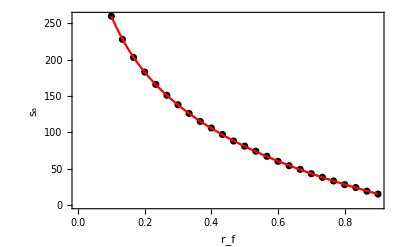

```mathematica
summaryIndex=1
ratioStart=1/10;
ratioEnd=9/10;

{accPlot,nlfPlot}=accuracyPlotOfR[seriesSummaryReport,summaryIndex,ratioStart,ratioEnd,baseSingularIndex,$theSingularList,baseSeries];
Show[{accPlot,nlfPlot}]
```

#### Manual accuracyPlotOf R

{1/10,2/15,1/6,1/5,7/30,4/15,3/10,1/3,11/30,2/5,13/30,7/15,1/2,8/15,17/30,3/5,19/30,2/3,7/10,11/15,23/30,4/5,5/6,13/15,9/10}

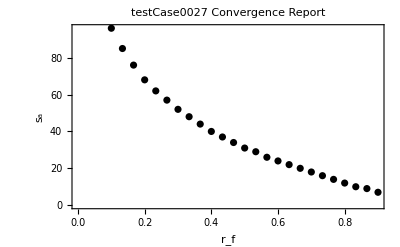

```mathematica
ratioStart=1/10;
ratioEnd=9/10;

ratioTable=Array[#&,{25},{ratioStart,ratioEnd}]
theRList=Abs[baseSingularPoint-$theSingularList[[#[[6]]]]]&/@ finalSummary;

branchIndexNumber=13;
generatorIndex=finalSummary[[branchIndexNumber,2,1]];

singPrec=Floor@Precision@$theSingularList;
zTable=Table[
zVal=rFactor  theRList[[branchIndexNumber]];
wp=Floor@Precision[$theFunction==0/.z->(baseSingularPoint+zVal)];
wVals=Sort[w/.NSolve[$theFunction==0/.z->(baseSingularPoint+zVal),w,WorkingPrecision->wp]];
bVal=baseSeries[[generatorIndex]]/.z->zVal;
difArray=Abs[bVal-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];

{rFactor,-MantissaExponent[difArray[[pos]]][[2]]},
{rFactor,ratioTable}
];

lp1=ListPlot[zTable[[All,{1,2}]],PlotStyle->Black,Frame->True,FrameLabel->{Style["r_f",14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]},PlotLabel->finalConvergenceReportHeader[[1,1]]]
```

```mathematica
nlfLog=NonlinearModelFit[zTable[[All,{1,2}]],a1+a2 Log[10,r],{a1,a2,a3},r]

nlfPlot=Plot[nlfLog[r],{r,rStart,rEnd},PlotStyle->Red];
Show[{nlfPlot,lp1},Frame->True,FrameLabel->{Style["r_f",14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]}]
resList=nlfLog["FitResiduals"];
estVariance=nlfLog["EstimatedVariance"];
Print[Style["Estimated variance: ",Red],Style[estVariance,Red]];
residuePlot=ListPlot[N[resList,20],PlotRange->All]
```

{{0.1,960.},{0.133333,900.},{0.166667,801.},{0.2,720.},{0.233333,651.},{0.266667,592.},{0.3,540.},{0.333333,493.},{0.366667,451.},{0.4,412.},{0.433333,376.},{0.466667,343.},{0.5,313.},{0.533333,284.},{0.566667,257.},{0.6,232.},{0.633333,208.},{0.666667,185.},{0.7,163.},{0.733333,142.},{0.766667,123.},{0.8,104.},{0.833333,86.},{0.866667,68.},{0.9,51.}}

### Section 5.2: Accuracy plot as function of order

Fit function: 2.26205+0.306564 x

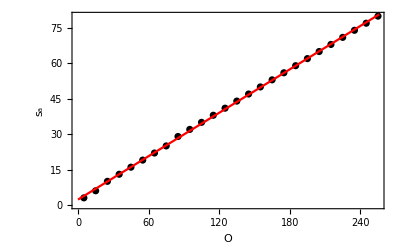

```mathematica
(*accuracyPlotOfO[finalSummary_,summaryIndex_,testRatio_,baseSingularIndex_,theSingularList_,baseSeries_] *)
theSummaryReportIndex=1;
plotData=accuracyPlotOfO[seriesSummaryReport,theSummaryReportIndex,1/2,baseSingularIndex,$theSingularList,baseSeries];
Show[plotData]
```

### Section 5.3: Accuracy plot as a function of theta

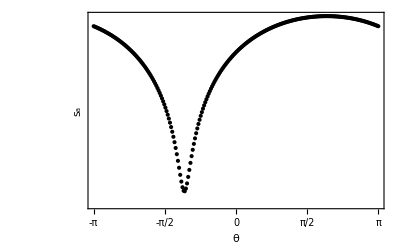

```mathematica
(* accuracyPlotOfT[finalSummary_,summaryIndex_,rRatio_,baseSingularIndex_,theSingularList_,baseSeries_] *)
theSummaryReportIndex=2;
accuracyPlotOfT[seriesSummaryReport,2,9/10,baseSingularIndex,$theSingularList,baseSeries]
```

#### Manual accuracy plot as function of theta

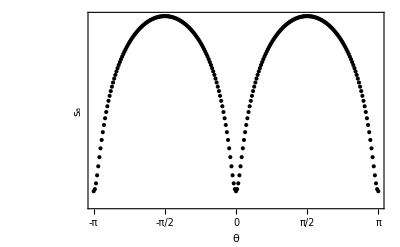

```mathematica
tStart=-Pi;
tEnd=Pi;
rVal=9/10;
thetaTable=Table[

zVal=rVal Exp[I theta];
wVals=Sort[w/.NSolve[theFunction==0/.z->(baseSingularPoint+zVal),w,WorkingPrecision->1500]];
bVal=baseSeries[[1]]/.z->zVal;
difArray=Abs[bVal-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];

pc=Floor@Precision@difArray;

{theta,-Log[difArray[[pos]]],pc},
{theta,tStart,tEnd,Pi/125}
];

lpTheta=ListLogPlot[thetaTable[[All,{1,2}]],PlotStyle->Black,Frame->True,FrameLabel->{Style["θ",14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]},FrameTicks->{{-π,-π/2,0,π/2,π},Automatic},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

## Section 6: Compute 3D-accuracy data

### Section 6.1: 3D accuracy user menu

```mathematica
accuracyAnalysisMenu=Column[{Style["3D-Accuracy Analysis Menu",16,Bold,Black],
Row[{Checkbox[Dynamic[$showBottomOutPoints]],Spacer[3],Style["Show limit accuracy points ",Black,Bold],Spacer[21],Checkbox[Dynamic[$customTickFlag]],Spacer[3],Style["Use custom plot ticks",Black,Bold]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold],Spacer[21],
Checkbox[Dynamic[$useRandomThetaFlag]],Spacer[3],Style["UseRandomTheta",Black,Bold]}]


},Frame->True,FrameStyle->Thick]
```

3D-Accuracy Analysis Menu
Show limit accuracy points Use custom plot ticks
Show plot label UseRandomTheta

### Section 6.2: Generate accuracy data as function of radius ratio and order

```mathematica
orderList=getOrderIndexes[baseSeries[[seriesSummaryReport[[All,4]]]]];
radiusRatioTable=Array[#&,25,{1/10,9/10}];
theRList=Abs[baseSingularPoint-$theSingularList[[#[[5]]]]]&/@ seriesSummaryReport;
argList=Array[#&,25,{-Pi,Pi}];

(*
 order list is {integer order, series term, actual order} elements
*)
finalOrderTable=Table[
orderList[[j,k]],
{j,1,Length@orderList},
{k,10,Length@orderList[[j]],Floor[Length@orderList[[j]]/25]}
];
finalOrderTable=Reverse[#]&/@ finalOrderTable;

accuracyData3D=generate3DAccuracyData[seriesSummaryReport,baseSingularPoint,baseSeries,baseSheetLinks,radiusRatioTable,theRList,argList,finalOrderTable];
```

Analyzing summaryIndex 1

Analyzing summaryIndex 2

low accuracy

low accuracy

low accuracy

«3 more identical outputs»

Total time to compute accuracy core: 0.199771 min.

#### Manual routine to generate 3D-accuracy data with bottom-out points

```mathematica
(*
 get orderList, ratioTable,theRList,argList
*)
orderList=getOrderIndexes[baseSeries[[finalSummary[[All,2,1]]]]];
ratioTable=Array[#&,25,{1/10,9/10}]
theRList=Abs[baseSingularPoint-$theSingularList[[#[[6]]]]]&/@ finalSummary;
Print["theRList: ",theRList//N];
argList=Array[#&,25,{-Pi,Pi}];
(*
 order list is {integer order, series term, actual order} elements
*)
finalOrderTable=Table[
orderList[[j,k]],
{j,1,Length@orderList},
{k,10,Length@orderList[[j]],Floor[Length@orderList[[j]]/25]}
];
finalOrderTable=Reverse[#]&/@ finalOrderTable;
finalOrderTable[[1]]
finalOrderTable[[1,All,2]]

bt=$showBottomOutPoints

at10=AbsoluteTiming[
accuracyData3D=ParallelTable[
If[theRatioIndex==1 && theOrderIndex==1,
Print["Analyzing summaryIndex ",summaryIndex];
];
currentOrderArray=finalOrderTable[[summaryIndex,theOrderIndex]];
currentIntegerOrder=currentOrderArray[[1]];
seriesEndTerm=currentOrderArray[[2]];
actualOrder=currentOrderArray[[3]];
branchSeriesIndex=baseSheetLinks[[summaryIndex,2,1]];

If[theOrderIndex==1,
(*zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]] Exp[RandomChoice[argList]I];*)
zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]] Exp[Pi I/4];
(* zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]]Exp[RandomChoice[argList] I];*)
bVal=baseSeries[[branchSeriesIndex,1;;seriesEndTerm]]/.z->zVal;
rootFunction=theFunction==0/.z->(baseSingularPoint+zVal);
rootFunctionPrecision=Floor@Precision@rootFunction;
Quiet[wVals=w/.NSolve[$theFunction==0/.z->(baseSingularPoint+zVal),w,WorkingPrecision->rootFunctionPrecision]];
difTable=Abs[#-bVal]&/@ wVals;
wPosArray=Flatten[Position[difTable,x_/;x==Min[difTable]]];
If[Length@wPosArray==0,
Print[Style["Error with wPosArray: ",Red],wPosArray," at order " ,currentIntegerOrder," for cycle ",finalSummary[[summaryIndex,3]]];
difTable=Abs[#-bVal]&/@ wVals;
minDif=Min[difTable];
loc2=Flatten[Position[difTable,x_/;x==minDif]][[1]];
theVal={"pa","pa","pa","pa","pa"};
,
wPos=wPosArray[[1]];
wMatch=wVals[[wPos]];
dif=Abs[bVal-wMatch];
If[Precision@dif<25,
Print[Style["low precision",Red]];
Print["dif: ",N[dif,10]];

If[$showBottomOutPoints,
theVal={ratioTable[[theRatioIndex]],actualOrder,Floor@Precision@baseSeries[[branchSeriesIndex]],Floor@Precision@baseSeries[[branchSeriesIndex]],Abs[zVal]};
,
theVal={"dp","dp","dp","dp","dp"};
];
,
me=-MantissaExponent[dif][[2]];
If[me<10,
Print["low accuracy"];
theVal={"a","a","a","a","a"};
,
theVal={ratioTable[[theRatioIndex]],actualOrder,me,Log[dif],Abs[zVal]};
];
];
]; (* *)
,
bVal=baseSeries[[branchSeriesIndex,1;;seriesEndTerm]]/.z->zVal;
dif=Abs[bVal-wMatch];
If[Precision@dif<25,
Print[Style["low preciison2",Red]];
If[$showBottomOutPoints,
theVal={ratioTable[[theRatioIndex]],actualOrder,Floor@Precision@baseSeries[[branchSeriesIndex]],Floor@Precision@baseSeries[[branchSeriesIndex]],Abs[zVal]};
,
theVal={"dp2","dp2","dp2","dp2","dp2"};
];
,
me=-MantissaExponent[dif][[2]];
If[me<1,
Print["low accuracy"];
theVal={"a","a","a","a","a"};
,
theVal={ratioTable[[theRatioIndex]],actualOrder,me,-Log[10,dif],Abs[zVal]};
];
];
]; (* *)

theVal,
{theRatioIndex,1,Length@ratioTable},
{summaryIndex,1,Length@finalSummary},
{theOrderIndex,1,Length@finalOrderTable[[summaryIndex]]}
];
];
Print["Total time to compute accuracy core: ",at10[[1]]/60.," min."]
```

### Generate 3D-accuracy point plot showing bottom-out precision points

```mathematica
(*
 generate bottom out accuracy  plot
*)

sumIndex=1;
list1=Flatten[accuracyData3D[[All,sumIndex,All]],1];
list2=list1[[All,{1,2,3}]];
finalPointList=Select[list2,VectorQ[#,NumericQ]&]//N;
accuracyPoints3DPlot=ListPointPlot3D[finalPointList,ColorFunction->Function[{x,y,z},Black],BoxRatios->{1, 1, 1},PlotRange->All,(*Ticks->{Automatic,{200,400,600,800},{200,400,600,800,900}},*)AxesLabel->{Style["r_f",14,Bold,Black],Style["Order",12,Bold,Black],Style["s_a",16,Bold,Black]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

### Section 6.3: Generate accuracy point-plot

```mathematica
summaryReportIndex=1;
 branchName=seriesSummaryReport[[summaryReportIndex,2]];
plotLabel=Column[{Style[$theTestCase],Style[branchName]},Alignment->Center];

list1=Flatten[accuracyData3D[[All,summaryReportIndex,All]],1];
list2=list1[[All,{1,2,3}]];
finalPointList=Select[list2,VectorQ[#,NumericQ]&]//N;
accuracyTempPlot=ListPointPlot3D[list2,ColorFunction->Function[{x,y,z},Black],BoxRatios->{1, 1, 1},PlotRange->All];

pRange=PlotRange[accuracyTempPlot];

rTicks=SetPrecision[Array[#&,{5},{pRange[[1,1]],pRange[[1,2]]}],1];

oTicks=Array[Floor@#&,{5},{pRange[[2,1]],pRange[[2,2]]}];

aTicks=Array[Ceiling@#&,{5},{pRange[[3,1]],pRange[[3,2]]}];

accuracyPoints3DPlot=ListPointPlot3D[list2,ColorFunction->Function[{x,y,z},Black],PlotRange->All,Ticks->{rTicks,oTicks,aTicks},AxesLabel->{Style["r_f",14,Black,Bold],Style[,12,Black,Bold],Style["s_a",16,Black,Bold]},
AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1, 1, 1}
]
```

-Graphics3D-

## Section 7: Generate non-linear fit models

### Section 7.1: Create accuracy fit models

```mathematica
accuracyModels=generateAccuracyModel[seriesSummaryReport,$theTestCase,accuracyData3D];
```

nlmf3D function: FittedModel[2.2433+m (0.00642408-0.43468 Log[r])-0.168551 Log[r]]

Estimated variance: 0.13224

The accuracy function: 2.2433+ord (0.00642408-0.43468 Log[r])-0.168551 Log[r]

The order function: Ceiling[(-2.2433+a+0.168551 Log[r])/(0.00642408-0.43468 Log[r])]

nlmf3D function: FittedModel[0.15873+m (0.00953337-0.434377 Log[r])-0.37378 Log[r]]

Estimated variance: 0.526389

The accuracy function: 0.15873+ord (0.00953337-0.434377 Log[r])-0.37378 Log[r]

The order function: Ceiling[(-0.15873+a+0.37378 Log[r])/(0.00953337-0.434377 Log[r])]

### Section 7.2: Extract accuracy and order functions from accuracy models

```mathematica
(* {avgSumPlot,accuracyPoints3DPlot,theC0,theC1,theC2,theC3,estVariance,residuePlot,accF[r,ord],orderF[r,a],minRadius,maxRadius,minOrder,maxOrder,finalPointList,{rTicks,oTicks,aTicks},pRange}*)

accuracyF[r_,ord_]=accuracyModels[[summaryReportIndex,9]]


orderF[r_,a_]=accuracyModels[[summaryReportIndex,10]]

reqOrder=orderF[1/2,100]
orderG=Graphics3D@{PointSize[0.025],Red,Point[{1/2,reqOrder,110}]};
```

2.2433+ord (0.00642408-0.43468 Log[r])-0.168551 Log[r]

Ceiling[(-2.2433+a+0.168551 Log[r])/(0.00642408-0.43468 Log[r])]

318

### Section 7.3: Create order contour: (r,75)

```mathematica
ppA=ParametricPlot3D[{r,orderF[r,15],15},{r,1/10,9/10},BoxRatios->{1, 1, 1},PlotStyle->Yellow]
```

-Graphics3D-

### Section 7.4: Plot accuracy model with accuracy points

```mathematica
Show[accuracyModels[[summaryReportIndex,{2}]],ImageSize->300]
Show[{accuracyModels[[summaryReportIndex,{1,2}]],ppA,orderG},ImageSize->300]
```

-Graphics3D-

-Graphics3D-

### Section 7.5: Create accuracy fit model and export to file

```mathematica
(* {avgSumPlot,accuracyPoints3DPlot,theC0,theC1,theC2,theC3,estVariance,residuePlot,accF[r,ord],orderF[r,a],minRadius,maxRadius,minOrder,maxOrder,finalPointList,{rTicks,oTicks,aTicks},pRange},*)

fitSummary=MapThread[{#1[[2]],#1[[5]],SetAccuracy[#1[[6]],4],#1[[8]],SetAccuracy[#2[[3]],4],SetAccuracy[#2[[4]],4],SetAccuracy[#2[[5]],4],SetAccuracy[#2[[6]],4],SetAccuracy[#2[[7]],4]}&,{seriesSummaryReport,accuracyModels}];
fitSummaryHeader={"Type","CLSP","R","Order","a","b","c","d","Var"};
Grid[Prepend[fitSummary,fitSummaryHeader],Dividers->{{{True}},{True,True,{False},True}}]

Print["Exporting nonlinear fit models to "<>nonLinearFitDataFileName[$theTestCase,baseSingularIndex]];
Export[nonLinearFitDataFileName[$theTestCase,baseSingularIndex],{fitSummary,fitSummaryHeader}];
```

Type | CLSP | R | Order | a | b | c | d | Var
V_2^1 | 6 | 0.477 | 256 | 2.243 | -0.169 | 0.006 | -0.435 | 0.132
T | 6 | 0.477 | 511 | 0.159 | -0.374 | 0.01 | -0.434 | 0.526

Exporting nonlinear fit models to D:\algFunctionBook\data\testCase0017\nonLinearFitData2.m

### Section 7.6: Plot order function in defined domain

```mathematica
genNum=1;
rStart=accuracyModels[[genNum,-2,1,1]]
```

0.1

```mathematica
(*
 plot order function
*)

(*
{avgSumPlot,accuracyPoints3DPlot,theC0,theC1,theC2,theC3,estVariance,residuePlot,accF[r,ord],orderF[r,a],minRadius,maxRadius,minOrder,maxOrder,finalPointList,{rTickArray,oTickArray,aTicks},pRange,finalPointList}
*)

genNum=2;
rStart=accuracyModels[[genNum,-2,1,1]];
rEnd=accuracyModels[[genNum,-2,1,2]];
oStart=accuracyModels[[genNum,-2,2,1]];
oEnd=accuracyModels[[genNum,-2,2,2]];
aStart=accuracyModels[[genNum,-2,3,1]];
aEnd=accuracyModels[[genNum,-2,3,2]];
orderF[r_,a_]=accuracyModels[[genNum,10]][[1]];
{rTicks,oTicks,aTicks}=accuracyModels[[genNum,16]]//N




orderFunctionPlot=Plot3D[orderF[r,a],{r,rStart,rEnd},{a,aStart,aEnd},PlotRange->All,ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.55],branchColors[[1]]},Ticks->{rTicks,aTicks,Automatic},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["r_f",14,Black],Style["s_a",16,Black],Style["",12,Black]}]
```

{{0.1,0.3,0.5,0.7,0.9},{10.,135.,260.,385.,510.},{0.,129.,258.,387.,515.}}

-Graphics3D-

### Section 7.7: Plot order function in extrapolated domain

```mathematica
orderFunctionPlot=Plot3D[orderF[r,a],{r,0.1,0.9},{a,1,250},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.55],branchColors[[1]]},Ticks->{rTicks,aTicks,Automatic},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["r_f",14,Black],Style["s_a",16,Black],Style["",12,Black]}]
```

-Graphics3D-

```mathematica
{rTickArray,oTickArray,aTicks}=accuracyModels[[genNum,-2]]//N
```

{{0.1,0.3,0.5,0.7,0.9},{10.,135.,260.,385.,510.},{0.,129.,258.,387.,515.}}

```mathematica
dataTable=Flatten[Table[

{rVal,aVal,orderF[rVal,aVal]},
{rVal,rStart,rEnd,(rEnd-rStart)/25},
{aVal,aStart,aEnd,(aEnd-aStart)/25}
],1];
(*{rTickArray,oTickArray,aTicks}=accuracyReportResults[[genNum,-3]];*)
{rTickArray,oTickArray,aTicks}=accuracyModels[[genNum,-2]];
dataTable[[1;;25]]//N
ListPointPlot3D[dataTable,PlotRange->{{rStart,rEnd},{aStart,aEnd},{oStart,oEnd}},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.55],branchColors[[1]]},Ticks->{rTickArray,aTicks,Automatic},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["r_f",14,Black],Style["s_a",16,Black],Style["",12,Black]}]

inverseIntF=Interpolation[dataTable];
inverseIntF[1/2,50]
Plot3D[inverseIntF[r,a],{r,rStart,rEnd},{a,aStart,aEnd},PlotRange->{{rStart,rEnd},{aStart,aEnd},{oStart,oEnd}},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.55],branchColors[[1]]},Ticks->{rTickArray,aTicks,Automatic},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["r_f",14,Black],Style["s_a",16,Black],Style["",12,Black]}]
```

{{0.1,0.,-1.00957},{0.1,5.16,4.10073},{0.1,10.32,9.21104},{0.1,15.48,14.3213},{0.1,20.64,19.4316},{0.1,25.8,24.542},{0.1,30.96,29.6523},{0.1,36.12,34.7626},{0.1,41.28,39.8729},{0.1,46.44,44.9832},{0.1,51.6,50.0935},{0.1,56.76,55.2038},{0.1,61.92,60.3141},{0.1,67.08,65.4244},{0.1,72.24,70.5347},{0.1,77.4,75.645},{0.1,82.56,80.7553},{0.1,87.72,85.8656},{0.1,92.88,90.9759},{0.1,98.04,96.0862},{0.1,103.2,101.197},{0.1,108.36,106.307},{0.1,113.52,111.417},{0.1,118.68,116.527},{0.1,123.84,121.638}}

-Graphics3D-

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction::femdmval: Input value {0.5,50.} lies outside the range of data in the interpolating function.

144.044

-Graphics3D-

## Section 8: Check fit models

```mathematica
(*
 routine to check accuracy functions
*)
 sumIndex=summaryReportIndex
theRatio=1/3;
desiredAccuracy=100
genIndex=baseSheetLinks[[sumIndex,2,1]];
Print["baseSheetLinks: ",baseSheetLinks[[sumIndex,2]]];

clsp=seriesSummaryReport[[sumIndex,5]];
bigR=Abs[baseSingularPoint-$theSingularList[[clsp]]];
Print["bigR: ",bigR//N];
zVal=theRatio bigR Exp[RandomChoice[argList] I];
Print["zVal: ",N[zVal,10]];
wVals=w/.NSolve[$theFunction/.z->(baseSingularPoint+zVal),w,WorkingPrecision->500];

accuracyF[r_,ord_]=accuracyModels[[sumIndex,9]];

Print["Accuracy function: ",accuracyF[r,ord]//N];

orderF[r_,a_]=accuracyModels[[sumIndex,10]]
Print["orderF[r,a]: ",orderF[r,a]];
requiredOrder=orderF[theRatio,desiredAccuracy];

fitAccG=Graphics3D@{PointSize[0.025],Green,Point@{theRatio,requiredOrder,accuracyF[theRatio,requiredOrder]}};
(*
 accuracy funtion point
*)
estAccPoint={theRatio,requiredOrder,desiredAccuracy};
estAccPoint3D=Graphics3D@{PointSize[0.025],Red,Point@estAccPoint};

Print["Required order for accuracy of ",desiredAccuracy," is ",requiredOrder];
accData=getOrderIndex3[requiredOrder,seriesSummaryReport,sumIndex];
If[accData=={"e","e"},
Print["getOrderIndex3 error"];
,
Print["Series term length for order ",requiredOrder," is ",accData[[2]]];

pVal=baseSeries[[genIndex,1;;accData[[2]]]]/.z->zVal;
difTable=Abs[#-pVal]&/@ wVals;
Print[difTable//N];

posArray=Position[wVals,x_/;Abs[x-pVal]<10^-10];
actualAccuracy=Abs[wVals[[posArray[[1,1]]]]-pVal];
Print["Actual accuracy: ",-MantissaExponent[actualAccuracy][[2]]];
actAccuracy=-MantissaExponent[actualAccuracy][[2]];
actAccPoint={theRatio,requiredOrder,actAccuracy};
actAccPoint3D=Graphics3D@{PointSize[0.025],Blue,Point@actAccPoint};
];
```

1

100

baseSheetLinks: {1,2}

bigR: 0.476781

zVal: -0.1376347933-0.079463485 ⅈ

Accuracy function: 2.2433+ord (0.00642408-0.43468 Log[r])-0.168551 Log[r]

Ceiling[(-2.2433+a+0.168551 Log[r])/(0.00642408-0.43468 Log[r])]

orderF[r,a]: Ceiling[(-2.2433+a+0.168551 Log[r])/(0.00642408-0.43468 Log[r])]

Required order for accuracy of 100 is 202

Series term length for order 202 is 404

{3.6818,2.7252×10^-101,1.0517}

Actual accuracy: 100

```mathematica
Show[{accuracyModels[[summaryReportIndex,{1,2}]],ppA},ImageSize->300]
```

-Graphics3D-

```mathematica
Show[{accuracyModels[[summaryReportIndex,{1,2}]],estAccPoint3D,actAccPoint3D,ppA},ImageSize->300]
```

-Graphics3D-

## Section 9: Generate interpolation function for accuracy profile function

### Section 9.1: User menu

```mathematica
segmentMenu=Column[{Style["3D-Accuracy Analysis Menu",16,Bold,Black],
Row[{Checkbox[Dynamic[$showBottomOutPoints]],Spacer[3],Style["Show limit accuracy points ",Black,Bold],Spacer[21],Checkbox[Dynamic[$customTickFlag]],Spacer[3],Style["Use custom plot ticks",Black,Bold]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold],Spacer[21]}]


},Frame->True,FrameStyle->Thick]
```

3D-Accuracy Analysis Menu
Show limit accuracy points Use custom plot ticks
Show plot label

```mathematica
Column[{convergenceSummaryHeader,Grid[convergenceSummaryReport,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]
```

testCase0017 Root Test results
Singular Index 2
Index | Name | Cycle
Size | Generator | CLSP | R | Series
Size | Order | Precision
1 | V_2^1 | 2 | 1 | 6 | 0.476781 | 512 | 256 | 988
2 | T | 1 | 3 | 6 | 0.476781 | 512 | 511 | 961

### Section 9.2: Create accuracy interpolation function

```mathematica
seriesReportIndex=1;
clspSingularPoint=$theSingularList[[seriesSummaryReport[[seriesReportIndex,5]]]];
clspSingularPoint//N

 (* {intFA,lpp3D,interpolatePlot,orderTableSave,plotTable,{orderStart,orderEnd},{radiusRatios[[1]],radiusRatios[[-1]]}} *)

interpolationData=getInterpolationFunction[seriesSummaryReport,baseSeries,baseSingularPoint,clspSingularPoint,seriesReportIndex,10,10,Pi/4];   

orderStart=interpolationData[[3,1]]
orderEnd=interpolationData[[3,2]]

ratioStart=interpolationData[[4,1]]
ratioEnd=interpolationData[[4,2]]

(* {intFA,plotTable,{orderStart,orderEnd},{radiusRatios[[1]],radiusRatios[[-1]]}} *)

intLines=MapThread[{#1,x,#2}&,{ interpolationData[[2,All,1]],interpolationData[[2,All,2,1]]}]
intPlot3D=Table[
ParametricPlot3D[intLines[[n]],{x,orderStart,orderEnd},PlotRange->All,PlotStyle->Black,AxesLabel->{Style["r_f",14,Black],Style[,12,Black],Style["I_a",16,Black,Bold,FontFamily->"Courier New"]},
AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1, 1, 1}],
{n,1,Length@intLines}
];
Length@intPlot3D
intFA=interpolationData[[1]]
```

0.199211-0.933168 ⅈ

rIndex: 1

NSolve::precw: The precision of the argument function ({(«1041»-«1041» ⅈ)+(«1042»-«1041» ⅈ) w^2+(«1040»-«1040» ⅈ) w^3}) is less than WorkingPrecision (1000).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

rIndex: 2

rIndex: 3

rIndex: 4

rIndex: 5

rIndex: 6

rIndex: 7

rIndex: 8

rIndex: 9

rIndex: 10

theF: 2.49567+1.00861 x

theF: 2.34402+0.732402 x

theF: 2.25978+0.564891 x

theF: 2.20642+0.444288 x

theF: 2.17102+0.349983 x

theF: 2.0503+0.272913 x

theF: 1.94547+0.207543 x

theF: 1.8634+0.150746 x

theF: 1.7972+0.100531 x

theF: 1.74263+0.0555302 x

5

256

1/10

9/10

{{1/10,x,2.49567+1.00861 x},{17/90,x,2.34402+0.732402 x},{5/18,x,2.25978+0.564891 x},{11/30,x,2.20642+0.444288 x},{41/90,x,2.17102+0.349983 x},{49/90,x,2.0503+0.272913 x},{19/30,x,1.94547+0.207543 x},{13/18,x,1.8634+0.150746 x},{73/90,x,1.7972+0.100531 x},{9/10,x,1.74263+0.0555302 x}}

10

InterpolatingFunction[…]

```mathematica
Show[{intPlot3D},BoxRatios->{1, 1, 1},ImageSize->300]
 interpolationPlot=Plot3D[interpolationData[[1]][r,o],{r,ratioStart,ratioEnd},{o,orderStart,orderEnd},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.25],Red},AxesLabel->{Style["r_f",14,Black,Bold],Style[,12,Black,Bold],Style["I_a",16,Black,Bold,FontFamily->"Courier New"]},
AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1, 1, 1}];
Show[{intPlot3D,interpolationPlot}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[{accuracyModels[[summaryReportIndex,{1,2}]],interpolationPlot,ppA},ImageSize->300]
```

-Graphics3D-

### Section 9.3: Check accuracy interpolation I_z(r_f,0)

```mathematica
(*
 routine to check accuracy functions
*)
 sumIndex=1;
theRatio=3/10;
theOrder=75
(*
 routine to estimate accuracy of selected series at r_f=theRatio, and order=theOrder and check against actual accuracy of series
*)

genIndex=baseSheetLinks[[sumIndex,2,1]]

clsp=seriesSummaryReport[[sumIndex,5]];
bigR=Abs[baseSingularPoint-$theSingularList[[clsp]]];

zVal=theRatio bigR Exp[RandomChoice[argList] I];

Print["zVal: ",N[zVal,10]];
wVals=w/.NSolve[$theFunction/.z->(baseSingularPoint+zVal),w,WorkingPrecision->500];

estAcc=intFA[theRatio,theOrder];
Print["estAcc: ",estAcc//N];

estAccPoint={theRatio,theOrder,estAcc};
estAccPoint3D=Graphics3D@{PointSize[0.025],Red,Point@estAccPoint};

accData=getOrderIndex3[theOrder,seriesSummaryReport,sumIndex]
pVal=baseSeries[[sumIndex,1;;accData[[2]]]]/.z->zVal;
Print["wVals: ",wVals//N];
Print["pVal: ",pVal//N];
difTable=Abs[#-pVal]&/@ wVals;
Print[difTable//N];

posArray=Position[wVals,x_/;Abs[x-pVal]<10^-10];
actualAccuracy=Abs[wVals[[posArray[[1,1]]]]-pVal];
Print["Actual accuracy: ",-MantissaExponent[actualAccuracy][[2]]];
actAccuracy=-MantissaExponent[actualAccuracy][[2]];
actAccPoint={theRatio,requiredOrder,actAccuracy};
actAccPoint3D=Graphics3D@{PointSize[0.025],Blue,Point@actAccPoint};
Show[{accuracyPoints3DPlot,interpolationPlot,estAccPoint3D}]
```

75

1

zVal: 0.0715171365-0.123871314 ⅈ

estAcc: 42.0801

{75,150,75}

wVals: {-2.6178-2.85801 ⅈ,-0.498636-0.181762 ⅈ,0.43411+0.186536 ⅈ}

pVal: -0.498636-0.181762 ⅈ

{3.41367,2.66081×10^-43,1.00282}

Actual accuracy: 42

-Graphics3D-

## Initialization

```mathematica
DistributeDefinitions[ z,
 w,
 $workingPrecision,
 $separationFactor,
 $showBottomOutPoints
];
```

```mathematica
(*
 Turn off all operator ligatures for old-style brackets (changes compact brackets to old-style [[]] brackets
*)
CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]={}



Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]


$HistoryLength=0;
$useRandomThetaFlag=False;

 ParallelEvaluate[Off[NSolve::precw ]]

 $workingPrecision=1000;
 $showBottomOutPoints=False; (* apparently need to distribute this flag in ParallelTable usage *)

 $customTickFlag=False;
 $showPlotLabel=False;
$acf=20;
$maxRootVerifyDifference=10^-50;

DistributeDefinitions[ z,
 w,
 $workingPrecision,
 $separationFactor,
 $showBottomOutPoints  (* apparently needed when using ParallelTable *)
];

 $userDirectory="D:\\puiseuxSeries";

DistributeDefinitions[ z, w]

colorNumbers={14,60,45,57,24,35,43};
theColorList=Flatten@Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,7}]

theColors=Join[{Red,Blue,Darker@Green,Purple,Black,Brown,Pink,Magenta},theColorList]
workingPrecision=1000;

stdColors= ColorData[97,"ColorList"]
branchColors= ColorData[97,"ColorList"]
```

{Null,Null,Null,Null}

{}

{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865],RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616],RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498],RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863],RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]}

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, Rational[2, 3], 0],RGBColor[0.5, 0, 0.5],GrayLevel[0],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0.5, 0.5],RGBColor[1, 0, 1],RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865],RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616],RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498],RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863],RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
theColorList
```

{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865],RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616],RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498],RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863],RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]}

```mathematica
minSeparation[theList_]:=Module[{i,testVal,remainder,netList},
netList={};
If[Length@theList>1,
For[i=1,i<=Length@theList,i++,
testVal=theList[[i]];
remainder=Delete[theList,i];
AppendTo[netList,Min[Abs[testVal-#]&/@ remainder]];
];
Min@netList
,
(* if only one number in list, set default min separation at 10^-4 *)
10^-4
]
];
```

### getRadialRange

```mathematica
getRadialRange[actR_,totalPoints_]:=Module[{rData,rExp,fData,uLimit,lLimit,theRange},
rData=RealDigits[actR//N];
rExp=rData[[2]];
If[rExp==0,
fData=FromDigits[rData[[1,1;;3]]];
uLimit=fData/1000;
,
fData=FromDigits[rData[[1,1;;3]]];
uLimit=fData/100;
];
lLimit=1/10 uLimit;
theRange=Array[#&,totalPoints,{lLimit,uLimit}];
{lLimit,uLimit,theRange}
];
```

### polyForm(poly,var)

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

### getSingleConvergenceTrend

```mathematica
getSingleConvergenceTrend[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList,correctCharLen},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
correctCharLen=Length@correctChar;
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen,correctCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSeries[theSeries_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=theSeries/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[theSeries,z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=theSeries[[1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];
For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendTemp2[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag},
charMin=500;
maxCharFlag=False;
errorFlag=False;

singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];

For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]]},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"S",0,0,seriesWChar}];
PrependTo[cTable2,{"A",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendTempSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];


errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];

For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
convertToChar[num_]:=Module[{sTest,s1,newS,newS2},
sTest=ToString@AccountingForm@num;
s1=StringTake[sTest,1];
If[s1=="(",
newS=StringReplacePart[sTest,"-",{1,1}];
newS2=StringDrop[newS,-1];
Characters@newS2
,
Characters@sTest
]
];
```

### getInvalidRecs

```mathematica
getInvalidRecs[sheetIndex_,radiusIndex_,arcIndex_]:=Module[{sheetData,radiusData,circleData,arcData,invalidTerms,seriesData,validRecs,invalidRecs,radiusRatio},
 sheetData=sheetAccuracyTable[[sheetIndex]];
(* radiusData holds all data for this current radius index *)
radiusData=sheetData[[radiusIndex]];
(* circleData holds all data for this radius *)
circleData=radiusData[[3]];
radiusRatio=radiusData[[1]];
(* arcData holds all series data for this arc *)
arcData=circleData[[arcIndex]];
seriesData=arcData[[3]];
validRecs=Flatten@Position[seriesData,rec_/;VectorQ[rec,NumericQ]];
invalidRecs=Complement[Range[Length@termArray],validRecs];
If[Length@invalidRecs==0,
Print["No invalid recs"];
,
Print["Invalid recs: ",invalidRecs];
];
invalidTerms=seriesData[[invalidRecs,1]];
{radiusRatio,invalidTerms}
];
```

### getSingularPoints2

```mathematica
getSingularPoints2[theFunction_,workingPrecision_]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,minRadiusArray,thePoleList,theReturn},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1};
}
,
theSingularSet=Sort[z/.NSolve[Simplify@Resultant[theFunction,D[theFunction,w],w]==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
If[Length@theSingularSet==0,
Print[Style["No singular points found",Red]];
theReturn={-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-50&];
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
If[Last@pExp>0,
thePoleList=DeleteDuplicates[z/.NSolve[poleFunction==0,z,WorkingPrecision->workingPrecision]];
,
thePoleList={};
];

polePositions=Flatten[(Position[theSingularList,x_/;Abs[x-#]<10^-50]&/@ thePoleList)];

If[Length@polePositions>0,
poleIndexes={#}&/@ polePositions;
,
poleIndexes={};
];

(*
 compute minArray of integration region around each singular point 
*)
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
minRadiusArray=nearestDist;
theReturn={theSingularList,thePoleList,poleIndexes,minRadiusArray};
];
];
];
theReturn
];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[cRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
cRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*cRules[z]]@toPowerBoxes[w]@cRules[w][f];
```

### getOrderIndex

```mathematica
getOrderIndex[orderVal_,generatorIndex_]:=Module[{seriesSizes,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos},
seriesSizes=finalSummary[[All,10]];
cycleExpList=Exponent[baseSeries[[genIndexes[[generatorIndex]]]],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={-1,-1};
,
nearestExp=nearestExpList[[1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={-1,-1};
,
pos=posArray[[1,1]];
If[pos==seriesSizes[[generatorIndex]],
Print["Reached max order of ",orderVal," for branch ",finalSummary[[generatorIndex,3]]," at ",seriesSizes[[generatorIndex]],"terms"];
Print["max order: ",orderVal];
theVals={"e","e"};
,
theVals={Abs[$theSingularList[[finalSummary[[generatorIndex,6]]]]-$theSingularList[[baseSingularIndex]]],pos}
];
];
];
theVals
];

getOrderIndex2[orderVal_,finalSummaryIndex_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex},
seriesIndex=baseSheetLinks[[finalSummaryIndex,2,1]];

seriesSize=Length@baseSeries[[seriesIndex]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={"e","e"};
,
nearestExp=nearestExpList[[1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"e","e"};
,
pos=posArray[[1,1]];
If[pos==seriesSize && orderVal>nearestExp,
Print["Requested order of branch ",finalSummary[[finalSummaryIndex,3]]," is greater than max series order ",nearestExp];
theVals={"e","e"};
,
theVals={Abs[$theSingularList[[finalSummary[[finalSummaryIndex,6]]]]-$theSingularList[[baseSingularIndex]]],pos}
];
];
];
theVals
];
(*
returns {radius, position in series for the orderVal}
 *)





(*
returns {position in series for the requested order, and the actual exponent } 
*)
```

### getMaxOrder

```mathematica
getMaxOrder[summaryIndex_]:=Module[{seriesIndex,cycleExpList},
seriesIndex=seriesSummaryReport[[summaryIndex,4]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];
{Floor@cycleExpList[[-1]],cycleExpList[[-1]]}
]
```

### getIntegerOrderIndexes

```mathematica
getIntegerOrderIndexes[2]
```

getIntegerOrderIndexes[2]

```mathematica
baseSheetLinks
```

baseSheetLinks

```mathematica
getIntegerOrderIndexes[finalSummaryIndex_]:=Module[{seriesIndex,cycleExpList,integerOrders,orderIndexes,nearestExpList,integerCycleExpList,theOrderTable,theMaxOrder,theMaxExp},
seriesIndex=baseSheetLinks[[finalSummaryIndex,2,1]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];

integerCycleExpList=Select[cycleExpList,IntegerQ];
(*
 check if less than 10 integer orders
*)

If[Length@integerCycleExpList<10,
Print[Style["Too few integer orders",Red],Style[" Reverting to closest fractional power",Red]];
theMaxOrder=getMaxOrder[finalSummaryIndex][[1]];

Print["max order: ",theMaxOrder];

theOrderTable=getOrderIndex3[#,finalSummaryIndex]&/@ Range[theMaxOrder];
,
theMaxOrder=getMaxOrder[finalSummaryIndex][[1]];
orderIndexes=Flatten@(Position[cycleExpList,x_/;x==#]&/@ integerCycleExpList);
theOrderTable=MapThread[{#1,#2,#3}&,{integerCycleExpList,orderIndexes,integerCycleExpList}]
];
theOrderTable
];
SetAttributes[getIntegerOrderIndexes,Listable]
```

### getRationalOrderIndexes

```mathematica
getRationalOrderIndexes[finalSummaryIndex_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex,maxExp,nearestIntegerMax,rationalIndexes},
seriesIndex=baseSheetLinks[[finalSummaryIndex,2,1]];

seriesSize=Length@baseSeries[[seriesIndex]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];
maxExp=cycleExpList[[-1]];
nearestIntegerMax=Nearest[cycleExpList,Floor@maxExp][[1]];
rationalIndexes=Table[
nearestExp=Nearest[cycleExpList,orderVal][[1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb","eb"};
,
pos=posArray[[1,1]];
theVals={orderVal,pos,cycleExpList[[pos]]};
];
theVals,
{orderVal,1,nearestIntegerMax}
];
rationalIndexes
];
```

### getOrderIndexes

```mathematica
getOrderIndexes[theSeries_]:=Module[{cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,maxExp,nearestIntegerMax,rationalIndexes},

cycleExpList=Exponent[theSeries,z,List];
maxExp=cycleExpList[[-1]];
nearestIntegerMax=Nearest[cycleExpList,Floor@maxExp][[1]];
rationalIndexes=Table[
nearestExp=Nearest[cycleExpList,orderVal][[1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb","eb"};
,
pos=posArray[[1,1]];
theVals={orderVal,pos,cycleExpList[[pos]]};
];
theVals,
{orderVal,1,nearestIntegerMax}
];
rationalIndexes
];
SetAttributes[getOrderIndexes,Listable]
```

### accuracyPlotOfR

```mathematica
accuracyPlotOfR[finalSummary_,summaryIndex_,ratioStart_,ratioEnd_,baseSingularIndex_,theSingularList_,baseSeries_]:=Module[{ratioTable,theRList,generatorIndex,singPrec,zTable,zVal,wp,wVals,bVal,difArray,pos,posArray,genIndex,return,reportHeader,basePoint,nflLog,nflPlot,a1,a2,a3},

basePoint=theSingularList[[baseSingularIndex]];
ratioTable=Array[#&,{25},{ratioStart,ratioEnd}];
theRList=Abs[basePoint-theSingularList[[#[[5]]]]]&/@ finalSummary;

posArray=Position[finalSummary[[All,1]],x_/;x==summaryIndex];
If[Length@posArray==0,
Print["Summary index out of range"];
return={"",""};
,
generatorIndex=finalSummary[[summaryIndex,4]];

singPrec=Floor@Precision@theSingularList;
zTable=Table[
zVal=rFactor  theRList[[generatorIndex]];
wp=Floor@Precision[$theFunction==0/.z->(basePoint+zVal)];
wVals=Sort[w/.NSolve[$theFunction==0/.z->(basePoint+zVal),w,WorkingPrecision->wp]];
bVal=baseSeries[[generatorIndex]]/.z->zVal;
difArray=Abs[bVal-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];

{rFactor,-MantissaExponent[difArray[[pos]]][[2]]},
{rFactor,ratioTable}
];
nflLog=NonlinearModelFit[zTable,a1+a2 Log[10,r],{a1,a2,a3},r];
Print["fit function: ",nflLog[r]//N];
nflPlot=Plot[nflLog[r],{r,ratioStart,ratioEnd},PlotStyle->Red];
reportHeader=Column[{$theTestCase,Row[{Style[baseSingularIndex],Style[", "],Style[finalSummary[[summaryIndex,3]]]}]},Alignment->Center];
return={ListPlot[zTable[[All,{1,2}]],PlotStyle->Black,Frame->True,FrameLabel->{Style["r_f",14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]}],nflPlot};
];
return
];
```

### accuracyPlotOofO

```mathematica
accuracyPlotOfO[finalSummary_,summaryIndex_,testRatio_,baseSingularIndex_,theSingularList_,baseSeries_]:=Module[{genIndex,rationalR,bLen,zVal,wp,wVals,bVal,difArray,pos,theOrders,maxOrderIndex,maxOrder,nextIndex,nextOrder,dif,pc,bTable,posArray,return,basePoint,nlf,nlfPlot,reportHeader},

basePoint=theSingularList[[baseSingularIndex]];
posArray=Position[finalSummary[[All,1]],x_/;x==summaryIndex];
If[Length@posArray==0,
Print["Summary index out of range"];
return={"",""};
,
genIndex=finalSummary[[summaryIndex,4]];
rationalR=Rationalize[finalSummary[[summaryIndex,6]],0];
bLen=Length@baseSeries[[genIndex]];
 zVal=testRatio rationalR;
wp=Floor@Precision[$theFunction==0/.z->(basePoint+zVal)];
wVals=Sort[w/.NSolve[$theFunction==0/.z->(basePoint+zVal),w,WorkingPrecision->wp]];
bVal=baseSeries[[genIndex]]/.z->zVal;
difArray=Abs[bVal-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];
theOrders=getIntegerOrderIndexes[summaryIndex];
maxOrderIndex=theOrders[[-1,3]];
maxOrder=theOrders[[-1,1]];

 bTable=Table[
nextIndex=theOrders[[orderIndex,2]];
nextOrder=theOrders[[orderIndex,1]];
dif=Abs[(baseSeries[[genIndex,1;;nextIndex]]/.z->zVal)-wVals[[pos]]];
pc=Floor@Precision@dif;
{nextOrder,-MantissaExponent[dif][[2]]},
{orderIndex,5,Length@theOrders,10}
];

nlf=NonlinearModelFit[bTable[[All,{1,2}]],a+b x,{a,b},x];
Print["Fit function: ",nlf[x]//N];
nlfPlot=Plot[nlf[x],{x,0,maxOrder},PlotStyle->Red];
reportHeader=Column[{$theTestCase,Row[{Style[baseSingularIndex],Style[", "],Style[finalSummary[[summaryIndex,3]]]}]},Alignment->Center];

return={ListPlot[bTable[[All,{1,2}]],PlotStyle->Black,Frame->True,FrameLabel->{Style[,14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]}],nlfPlot};
];
return
]
```

### accuracyPlotOfT

```mathematica
accuracyPlotOfT[finalSummary_,summaryIndex_,rRatio_,baseSingularIndex_,theSingularList_,baseSeries_]:=Module[{bPoint,thetaTable,zVal,wVals,bVal,difArray,pos,generatorIndex,theR},

generatorIndex=finalSummary[[summaryIndex,4]];

bPoint=theSingularList[[baseSingularIndex]];
theR=Abs[bPoint-theSingularList[[finalSummary[[summaryIndex,5]]]]];
thetaTable=Table[
zVal=rRatio theR Exp[I theta];
wVals=Sort[w/.NSolve[$theFunction==0/.z->(bPoint+zVal),w(*,WorkingPrecision->1500*)]];
bVal=baseSeries[[generatorIndex]]/.z->zVal;
difArray=Abs[bVal-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];
{theta,-Log[difArray[[pos]]],pos},
{theta,-Pi,Pi,Pi/125}
];

ListLogPlot[thetaTable[[All,{1,2}]],PlotStyle->Black,Frame->True,FrameLabel->{Style["θ",14,Bold,Black],Rotate[Style["s_a",16,Black,Bold],-90 Degree]},FrameTicks->{{-π,-π/2,0,π/2,π},Automatic},FrameTicksStyle->Directive[Black,12,Black,Bold]]
];
```

### generate3DAccuracyData

```mathematica
(*
 get orderList, ratioTable,theRList,argList
*)
generate3DAccuracyData[finalSummary_,baseSingularPoint_,baseSeries_,(*theSingularList_,*)baseSheetLinks_,ratioTable_,theRList_,argList_,finalOrderTable_]:=Module[{accuracyData3D,currentOrderArray,currentIntegerOrder,seriesEndTerm,actualOrder,branchSeriesIndex, zVal,bVal,rootFunction,rootFunctionPrecision,wVals,difTable,wPosArray,minDif,loc2,theVal, wPos,wMatch,dif,me,at10},

(*   *)
at10=AbsoluteTiming[
accuracyData3D=ParallelTable[
If[theRatioIndex==1 && theOrderIndex==1,
Print["Analyzing summaryIndex ",summaryIndex];
];
currentOrderArray=finalOrderTable[[summaryIndex,theOrderIndex]];
currentIntegerOrder=currentOrderArray[[1]];
seriesEndTerm=currentOrderArray[[2]];
actualOrder=currentOrderArray[[3]];
branchSeriesIndex=baseSheetLinks[[summaryIndex,2,1]];
(* *)
If[theOrderIndex==1,
If[$useRandomThetaFlag,
zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]] Exp[RandomChoice[argList]I];
,
zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]] Exp[Pi I/4];
];
(* zVal=ratioTable[[theRatioIndex]] theRList[[summaryIndex]]Exp[RandomChoice[argList] I];*)
bVal=baseSeries[[branchSeriesIndex,1;;seriesEndTerm]]/.z->zVal;
rootFunction=$theFunction==0/.z->(baseSingularPoint+zVal);
rootFunctionPrecision=Floor@Precision@rootFunction;
Quiet[wVals=w/.NSolve[$theFunction==0/.z->(baseSingularPoint+zVal),w,WorkingPrecision->rootFunctionPrecision]];
difTable=Abs[#-bVal]&/@ wVals;
wPosArray=Flatten[Position[difTable,x_/;x==Min[difTable]]];
If[Length@wPosArray==0,
Print[Style["Error with wPosArray: ",Red],wPosArray," at order " ,currentIntegerOrder," for branch ",finalSummary[[summaryIndex,2]]];
difTable=Abs[#-bVal]&/@ wVals;
minDif=Min[difTable];
loc2=Flatten[Position[difTable,x_/;x==minDif]][[1]];
theVal={"pa","pa","pa","pa","pa"};
,

wPos=wPosArray[[1]];
wMatch=wVals[[wPos]];
dif=Abs[bVal-wMatch];
If[Precision@dif<25,
(*Print[Style["Precision of difTable <25",Red]];*)
Print["dif: ",N[dif,10]];
If[$showBottomOutPoints,
theVal={ratioTable[[theRatioIndex]],actualOrder,Floor@Precision@baseSeries[[branchSeriesIndex]],Floor@Precision@baseSeries[[branchSeriesIndex]],Abs[zVal]};
,
theVal={"dp","dp","dp","dp","dp"};
];
,
me=-MantissaExponent[dif][[2]];
If[me<10,
Print["low accuracy"];
theVal={"a","a","a","a","a"};
,
theVal={ratioTable[[theRatioIndex]],actualOrder,me,Log[dif],Abs[zVal]};
];
];
]; (* *)
,
(* *)
bVal=baseSeries[[branchSeriesIndex,1;;seriesEndTerm]]/.z->zVal;
dif=Abs[bVal-wMatch];
If[Precision@dif<25,
(*Print[Style["Precision of difTable <25",Red]];*)
If[$showBottomOutPoints,
theVal={ratioTable[[theRatioIndex]],actualOrder,Floor@Precision@baseSeries[[branchSeriesIndex]],Floor@Precision@baseSeries[[branchSeriesIndex]],Abs[zVal]};
,
theVal={"dp2","dp2","dp2","dp2","dp2"};
];
,
me=-MantissaExponent[dif][[2]];
If[me<1,
Print["low accuracy"];
theVal={"a","a","a","a","a"};
,
theVal={ratioTable[[theRatioIndex]],actualOrder,me,-Log[10,dif],Abs[zVal]};
];
];
]; (* *)

theVal,
{theRatioIndex,1,Length@ratioTable},
{summaryIndex,1,Length@finalSummary},
{theOrderIndex,1,Length@finalOrderTable[[summaryIndex]]}
];
];
Print["Total time to compute accuracy core: ",at10[[1]]/60.," min."];
accuracyData3D
]
```

### generateAccuracyModel

```mathematica
generateAccuracyModel[finalSummary_,theTestCase_,accuracyData3D_]:=Module[{accuracyModels,branchName,plotLabel,list1,list2,finalPointList,accuracyTempPlot,pRange,rTicks,rTickArray,oTicks,oTickArray,aTicks,aTickArray,accuracyPoints3DPlot,maxOrderIndex,minOrderIndex,nlmf,nlmfPlot,accF,orderF,maxOrder,minOrder,minRadius,maxRadius,theC0,theC1,theC2,theC3,estVariance,resList,residuePlot},


 accuracyModels=Table[
branchName=finalSummary[[theSummaryIndex,2]];
plotLabel=Column[{Style[theTestCase],Style[branchName]},Alignment->Center];

list1=Flatten[accuracyData3D[[All,theSummaryIndex,All]],1];
list2=list1[[All,{1,2,3}]];
finalPointList=Select[list2,VectorQ[#,NumericQ]&]//N;
accuracyTempPlot=ListPointPlot3D[finalPointList,ColorFunction->Function[{x,y,z},Black],BoxRatios->{1, 1, 1}];
(*
 generate branchPoints for all branches and find non-linear fit for all the data 
*)
pRange=PlotRange[accuracyTempPlot];


If[$customTickFlag,

rTicks=SetPrecision[Array[#&,{5},{pRange[[1,1]],pRange[[1,2]]}],1];
rTickArray={#1,Column[{#1,SetPrecision[#1 theRList[[theSummaryIndex]],2]}]}&/@ rTicks;

oTicks=Array[#&,{5},{pRange[[2,1]],pRange[[2,2]]}];
oTickArray={#1,Ceiling@#1}&/@ oTicks;

aTicks=Array[Ceiling@#&,{5},{pRange[[3,1]],pRange[[3,2]]}];
aTickArray={#1,Ceiling@#1}&/@ aTicks;

accuracyPoints3DPlot=ListPointPlot3D[finalPointList,ColorFunction->Function[{x,y,z},Black],BoxRatios->{1, 1, 1},PlotRange->All,Ticks->{rTickArray,oTickArray,aTicks},AxesLabel->{Style["r",14,Black,Bold],Style[,12,Black,Bold],Style["s_a",16,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1, 1, 1},PlotRange->All,
PlotLabel->If[$showPlotLabel,plotLabel,None]];
,
 (* use default ticks *)
rTicks=SetPrecision[Array[#&,{5},{pRange[[1,1]],pRange[[1,2]]}],1];

oTicks=Array[Floor@#&,{5},{pRange[[2,1]],pRange[[2,2]]}];

aTicks=Array[Ceiling@#&,{5},{pRange[[3,1]],pRange[[3,2]]}];

accuracyPoints3DPlot=ListPointPlot3D[finalPointList,ColorFunction->Function[{x,y,z},Black],BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Ticks->{rTicks,oTicks,aTicks},AxesLabel->{Style["r_f",14,Black,Bold],Style[,12,Black,Bold],Style["s_a",16,Black,Bold]},PlotLabel->If[$showPlotLabel,plotLabel,None]];


];

maxOrderIndex=Max@finalOrderTable[[theSummaryIndex,All,3]];
minOrderIndex=Min@finalOrderTable[[theSummaryIndex,All,3]];
nlmf=NonlinearModelFit[finalPointList,(a+b Log[r]+m(c+d Log[r])),{a,b,c,d},{r,m}];

nlmfPlot=Plot3D[nlmf[r,m],{r,pRange[[1,1]],pRange[[1,2]]},{m,pRange[[2,1]],pRange[[2,2]]},PlotRange->pRange, BoxRatios->{1, 1, 1},PlotStyle->{LightBlue},
Ticks->{rTicks,oTicks,aTicks},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1, 1, 1},PlotRange->All,AxesLabel->{Style["r_f",14,Black,Bold],Style["",12,Black,Bold],Style["s_a",16,Black,Bold]},PlotLabel->If[$showPlotLabel,plotLabel,None]];


(* accuracyPoints3DPlot,maxOrderIndex,minOrderIndex,nlmf,avgSumPlot,accF,orderF*)


(*  *)
Print["nlmf3D function: ",nlmf//N];
resList=nlmf["FitResiduals"];
estVariance=nlmf["EstimatedVariance"];
Print[Style["Estimated variance: ",Red],Style[estVariance,Red]];
residuePlot=ListPlot[N[resList,20],PlotRange->All];

{theC0,theC1,theC2,theC3}=Quiet[nlmf["ParameterTableEntries"][[All,1]]];

accF[r_,ord_]:=theC0+theC1 Log[r]+ord(theC2+theC3 Log[r]);
Print["The accuracy function: ", N[accF[r,ord],20]];

orderF[r_,a_]:=Ceiling[(a-theC0-theC1 Log[r])/(theC2+theC3 Log[r])];
Print["The order function: ",orderF[r,a]];

(* *)


maxOrder=Max@finalOrderTable[[theSummaryIndex,All,3]];
minOrder=Min@finalOrderTable[[theSummaryIndex,All,3]];
minRadius=radiusRatioTable[[1]];
maxRadius=radiusRatioTable[[-1]];

{nlmfPlot,accuracyPoints3DPlot,theC0,theC1,theC2,theC3,estVariance,residuePlot,accF[r,ord],orderF[r,a],minRadius,maxRadius,minOrder,maxOrder,finalPointList,{rTicks,oTicks,aTicks},pRange},
{theSummaryIndex,1,Length@finalSummary}
];
accuracyModels
];
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singulardata.m"}]
resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m"}];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m"}];
branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }];
rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}];

finalConvergenceReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\finalConvergenceReportData`2`.m"][testCase,ToString@sing]}];

nonLinearFitDataFileName[testCase_String,sing_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"nonLinearFitData`2`.m"][testCase,ToString@sing]}];
```

### accuracyInterpolation

```mathematica
accuracyInterpolation[finalSummary_,baseSeries_,baseSingularPoint_,theSingularList_,summaryReportIndex_,radiusRatioArraySize_,orderArraySize_,theta_]:=Module[{theOrders,orderStart,orderEnd,theR,theRadiusArray,theOrderArray,generatorIndex,theTheta,radiusIndex,plotTable,theOrderErrorTable,theRadius,zVal,pVal,wVals,wValsPrec,errTable,minError,pos,cTable,dataVals,plotXStart,plotXEnd,linearLine,quadraticLine,cubicLine,linearResidue,cubicResidue,quadraticResidue,residueSet,functionList,bestPos,bestUpperFitPlot,bestUpperFitFunction,bestLowerFitPlot,bestLowFitFunction,bestFitPos,bestLowerFitFunction,lowerFitData,c0,c1,c2,c3},

theOrders=getOrderIndexes[baseSeries[[finalSummary[[summaryReportIndex,4]]]]];

orderStart=theOrders[[25,1]];
orderEnd=theOrders[[-1,1]];

theR=Abs[baseSingularPoint-theSingularList[[finalSummary[[summaryReportIndex,5]]]]];

theRadiusArray=Array[#&,radiusRatioArraySize,{1/10,9/10}];
Print["theRadiusArray: ",theRadiusArray];
theOrderArray=DeleteDuplicates@Array[Floor@#&,orderArraySize,{orderStart,orderEnd}];
Print["theOrderArray: ",theOrderArray];

generatorIndex=finalSummary[[summaryReportIndex,4]];

theTheta=SetPrecision[Rationalize[theta,0],1000];
branchName=finalSummary[[summaryReportIndex,2]];
Print["Analyzing branch ",branchName];

radiusIndex=0;
plotTable=Table[
radiusIndex++;

If[Mod[radiusIndex,1]==0,
Print["rIndex: ",radiusIndex];
];
 theOrderErrorTable=Table[
theRadius=radiusRatio theR;
zVal=SetPrecision[theRadius Exp[I (theTheta)],1000];

pVal=baseSeries[[generatorIndex,1;;theOrders[[orderIndex,2]]]]/.z->zVal;

If[orderIndex==theOrderArray[[1]],
wVals=w/.NSolve[$theFunction==0/.z->(baseSingularPoint+zVal),WorkingPrecision->Floor@Precision@baseSeries];
wValsPrec=Floor@Precision@wVals;
];
errTable=Abs[#-pVal]&/@ wVals;
minError=Min@errTable;
If[minError<10^-(wValsPrec-50),
Print[Style["Minimum difference approaching working precision",Red]];
Print["minError: ",N[minError,10]];
];
pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
If[Precision@errTable[[pos]]<10,
Print[Style["Minimum difference precision approaching zero",Red]];
Print[Style["Flagging maximum accuracy point NULL",Red]];
{radiusRatio,orderIndex,"np"}
,
{radiusRatio,orderIndex,-Log[10,errTable[[pos]]]}
],
{orderIndex,theOrderArray}

];


cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
 (* 
   Fit data to upper minimize function
 *)
linearLine=c0+c1 x/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

bestUpperFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
bestUpperFitFunction=functionList[[bestFitPos]];
  (* 
   Fit data to lower minimize function
 *)
cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
linearLine=c0+c1 x/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
(*  *)



bestLowerFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Black}];
bestLowerFitFunction=functionList[[bestFitPos]];
lowerFitData=Table[{radiusRatio,x,bestLowerFitFunction},{x,orderStart,orderEnd,(orderEnd-orderStart)/50}];


{radiusRatio,{bestLowerFitFunction,bestUpperFitPlot},{bestUpperFitFunction,bestLowerFitPlot},theOrderErrorTable,lowerFitData},
{radiusRatio,theRadiusArray}
];
plotTable
];
```

### getInterpolationFunction

```mathematica
getInterpolationFunction[seriesSummaryReport_,baseSeries_,baseSingularPoint_,clspSingularPoint_,summaryReportIndex_,radiusRatioArraySize_,orderStepSize_,theTheta_]:=Module[{theOrders,theOrderArray,orderStart,orderEnd,radiusRatios,seriesIndex,theR,plotTable,theOrderErrorTable,theRadius,zVal,pVal,wVals,errTable,minError,pos,cTable,dataVals,plotXStart,plotXEnd,linearLine,bestUpperFitPlot,bestUpperFitFunction,bestLowerFitPlot,bestLowerFitFunction,plot5Data,theF,lpp3D,intFA,interpolatePlot,orderTableSave,c0,c1},

theOrders=getOrderIndexes[baseSeries[[seriesSummaryReport[[summaryReportIndex,4]]]]];
theOrderArray=theOrders[[5;;Length[theOrders];;orderStepSize]] ;
orderStart=theOrderArray[[1,3]];
orderEnd=theOrders[[-1,3]];


radiusRatios=Array[#&,radiusRatioArraySize,{1/10,9/10}];

seriesIndex=seriesSummaryReport[[summaryReportIndex,4]];
theR=Abs[baseSingularPoint-clspSingularPoint];
(*
do plot table: theR,plotTable,theOrderErrorTable,theRadius,zVal,pVal,wVals,errTable,minError
*)
plotTable=Table[
Print["rIndex: ",radiusIndex];

 theOrderErrorTable=Table[
theRadius=(radiusRatios[[radiusIndex]] theR);
(*Print["theRadius: ",theRadius//N];*)
zVal=SetPrecision[theRadius Exp[I (theTheta)],1000];

pVal=baseSeries[[seriesIndex,1;;theOrderArray[[orderIndex,2]]]]/.z->zVal;

wVals=w/.NSolve[$theFunction==0/.z->(baseSingularPoint+zVal),WorkingPrecision->1000];
errTable=Abs[#-pVal]&/@ wVals;
minError=Min@errTable;

(*If[minError>10^-10,
Print[Style["Error approaching working precision",Red]];
Print["minError: ",minError//N];
]; 
*)
pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{radiusRatios[[radiusIndex]],theOrderArray[[orderIndex,3]],-Log[10,errTable[[pos]]]},
{orderIndex,1,Length@theOrderArray}
];
cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
 (* 
   Fit data to upper minimize function
 *)
linearLine=c0+c1 x/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;

bestUpperFitPlot=Plot[linearLine[x],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
bestUpperFitFunction=linearLine;
  (* 
   Fit data to lower minimize function 
 *)
cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];

linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;


bestLowerFitPlot=Plot[linearLine[x],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Black}];
bestLowerFitFunction=linearLine;


{radiusRatios[[radiusIndex]],{bestLowerFitFunction,bestLowerFitPlot},{bestUpperFitFunction,bestUpperFitPlot},theOrderErrorTable},
{radiusIndex,1,Length@radiusRatios}
];
(*
 now generate interpolated plot 
*)
 plot5Data=Table[
theF[x_]=plotTable[[rIndex,2,1]];
Print["theF: ",theF[x]//N];
Table[
{plotTable[[rIndex,1]],x,plotTable[[rIndex,2,1]]},
{x,orderStart,orderEnd,2}
],
{rIndex,1,Length@plotTable}
];

 intFA=Interpolation[Flatten[plot5Data,1]];
{intFA,plotTable,{orderStart,orderEnd},{radiusRatios[[1]],radiusRatios[[-1]]}}
];
```

### getSingularPoints

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
  getSingularPoints[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,rNormArray,singularPerimeters,singularNorms,singularDistances
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];
minRadiusArray=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];

singularPerimeters=minRadiusArray;
singularNorms=rNormArray;
singularDistances=nearestDistArray;





For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray={10/3};
nearestDistArray={10};
rNormArray={5};
singularPerimeters=10/3;
singularNorms=5;
singularDistances=10;

];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$acf;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### gretOrderIndex3

```mathematica
getOrderIndex3[orderVal_,summaryTable_,finalSummaryIndex_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex},
seriesIndex=summaryTable[[finalSummaryIndex,4]];

seriesSize=Length@baseSeries[[seriesIndex]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={"ea","ea"};
,
nearestExp=nearestExpList[[1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb"};
,
pos=posArray[[1,1]];
If[pos==seriesSize && orderVal>Round@nearestExp,
Print[Style["Requested order of branch ",Red],Style[seriesSummaryReport[[finalSummaryIndex,2]],Red],Style[" is greater than max series order ",Red],Style[Round@nearestExp,Red]];
theVals={"e","e"};
,
theVals={orderVal,pos,cycleExpList[[pos]]}
];
];

];
theVals
];
```